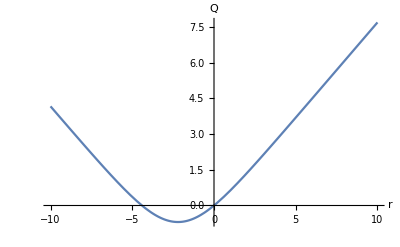

```mathematica
z0= 1/(√2);
Q[r_, z_] = 2Log[ Cosh[r] + z Sinh[r]];
q0[x_] = Q[x,z0];
Plot[Q[0.4x,z0], {x,-10,10},AxesLabel->{"r", "Q"}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Log[(2 ⅇ^(x/2)-√(-2+4 ⅇ^x))/(2+√2)]

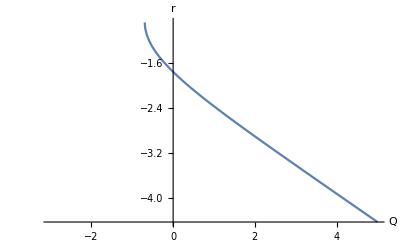

```mathematica
fInv[x_] = InverseFunction[q0][x]
Plot[{fInv[t]}, {t,-3,5},AxesLabel->{ "Q","r"}]
```

(z Cosh[r]+Sinh[r])/(Cosh[r]-z Sinh[r])

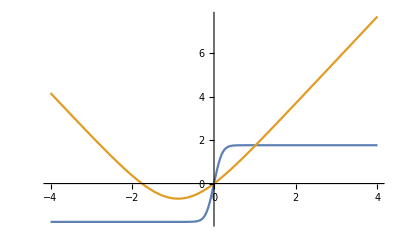

```mathematica
s=0.4;
zf[r_, z_] = (Sinh[r] + z Cosh[r])/(Cosh[r] -z Sinh[r])
Pf[r_,z_] = (1+z)/2 Exp[(-(r-1)^2)/(2 s^2)] + (1-z)/2 Exp[(-(r+1)^2)/(2 s^2)];
Pb[r_,z_] = (1+zf[r,z])/2 Exp[(-(-r-1)^2)/(2 s^2)] + (1-zf[r,z])/2 Exp[(-(-r+1)^2)/(2 s^2)];
Plot[{Log[Pf[x,z0]/Pb[x,z0]], Q[ x,z0]}, {x,-4,4}]
```